```mathematica
Clear[AllData, ZoomedData]
```

```mathematica
AllData = Import["dataWSM_x_PBC_y_PBC_Quasi+8and+6Irrationalm=0Parent32x32.dat"];
```

```mathematica
ZoomedData = Import["dataWSMZoomed_x_PBC_y_PBC_Quasi+8and+6Irrationalm=0Parent32x32.dat"];
```

```mathematica
B=Show[ListPlot[ZoomedData,PlotRange-> { All ,{-0.8,0.8}},PlotStyle->{PointSize[0.01],Black}],FrameTicks-> {{π/2},{-0.5,0,0.5},{},{}},BaseStyle-> 12,(** FrameLabel-> {"k_z","E"}, **)Frame-> True,RotateLabel-> False,FrameStyle->{{Thick, Black},{Thick, Black},{Thick, Black},{Thick, Black}},Axes->{True, False},
ImageSize-> 100]
```

-Graphics-

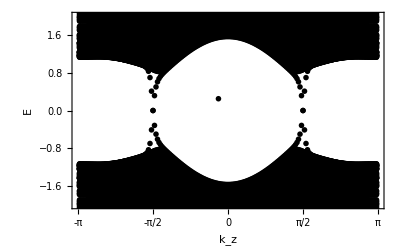

```mathematica
A=Show[ListPlot[AllData,PlotRange-> { {-π,π} ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}},BaseStyle-> 18,FrameLabel-> {"k_z","E"},Frame-> True,RotateLabel-> False,FrameStyle->{{Thick, Black},{Thick, Black},{Thick, Black},{Thick, Black}},Axes->{True, False},
Epilog-> Inset[B,{-0.2,0.25}]]
```